```mathematica
A = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 2}]
```

{37,7,26,27,91,77,58,87,58,13,62,91,18,18,23,61,90,26,2,54,27,30,52,39,3,37,32,43,28,6,50,50,71,45,37,19,84,61,46,51,39,95,16,27,28,89,54,98,98,61}

```mathematica
B = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 3}]
```

{25,88,65,5,28,51,29,83,10,98,52,26,68,64,3,6,39,53,96,15,40,24,65,27,84,13,83,43,14,65,76,95,15,100,5,62,92,58,10,32,9,83,41,99,46,32,19,1,13,39}

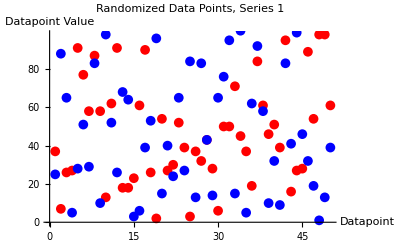

```mathematica
Show[ListPlot[A, PlotMarkers->{Automatic, Medium}, PlotStyle->Red], ListPlot[B, PlotMarkers->{Automatic, Medium}, PlotStyle->Blue],AxesLabel->{HoldForm[Datapoint],HoldForm[Datapoint Value]},PlotLabel->RawBoxes[RowBox[{RowBox[{"Randomized"," ","Data"," ","Points"}],","," ",RowBox[{"Series"," ","1"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%96,ImageSize->Full]
```

-Graphics-

```mathematica
?ImageSize
```